Symbolic Expressions

```mathematica
Today
```

Sat 21 Apr 2018

## Everything is an expression

Mathematica and the Wolfram programming language are a powerful computation engine to simplify arbitrary expressions that may or may not be about mathematics. Its built-in knowledge base contains tons of simplification rules currently known to humanity drawn from all over the realm of mathematics. From this repeated simplification of expressions, computation emerges in the sense that any problem that can be algorithmically solved using a more traditional programming language can also be solved with Mathematica.

Mathematica "programs" are written in literate programming style as interactive notebooks like the one that you are reading right now. Each notebook consists of cells that are arranged together sequentially and hierarchically. Individual cells can be either plain text paragraphs that don't get evaluated but are displayed as given, or Mathematica input expressions. To enter the next cell when editing the current one, just move the cursor key down past your current cell. At the end of the notebook and between individual cells, the Mathematica front end offers controls to add new cells of various types, and combine and modify the existing cells and their contents.

The actual computations are done by the internal part of Mathematica called the kernel. The kernel remembers all the definitions that you have made so far, as it also remembers the results that your computations have produced. The kernel performs the actual computations behind the scenes on command, and returns the results for the front end to display to the users. You can have any number of notebooks simultaneously open in the front end, all handled by either the same or different kernels. It is important to understand the distinction between the front end notebooks and the kernel chugging under the hood, because definitions made in different notebooks but executed by the same kernel can clash with each other, if the same symbol is unintentionally used to mean different things. (Then again, this problem is shared by the entire physical reality, not just the small part of it that you think of as your “computer”.)

Before we start, let us tell Mathematica to clear everything. This notebook has been open quite a while I have been writing this, and a bunch of other notebooks have been open at the same time. The next function call is how you always get to start from a blank slate, at least in Mathematica if not in life in general. (Alternatively, you could go to the "Evaluation" menu and first select "Quit Kernel", then go to the same menu and start a new fresh kernel.)

```mathematica
ClearAll["Global`*"]
```

When editing a Mathematica document, pressing CTRL-ENTER gives the current input form cell to the kernel for evaluation and gives it a running number that can later be used to refer to that cell. The result is shown as an output cell with the same running number, placed after the input form cell that produced it. Alternatively, you can select “Evaluate Notebook” in the “Evaluation” menu to tell Mathematica to evaluate all the cells of your notebook in the order in which they appear in the document. Here is our first proper input form cell to do a very simple computation. For ordinary arithmetic, simplification of symbolic expressions corresponds to their familiar evaluation.

```mathematica
2+2
```

4

Nothing fancy here, any old programming language could do this. Simplifying formulas that consist of mathematical symbols produces a result that contains those symbols... and sometimes your expression is already in the simplest possible form, so the simplification effectively does nothing because the expression is already its own answer. (As an important general principle in all of programming, whenever there is nothing to do, the correct thing to do is to do nothing.)

```mathematica
Sqrt[π + E + Sin[1/3]]
```

√(ⅇ+π+Sin[1/3])

To enter special characters such as π, press ESC, type in the special code for that character (all these codes are easily found with Google), and press ESC again. When the Mathematica front end displays the result of simplifying an expression, it uses its built-in formatting rules to pretty print the formula in a way that is more satisfying and easier to understand for us humans. In reality, under the hood, the result is still a symbolic expression.

```mathematica
FullForm[%]
```

Power[Plus[E,Pi,Sin[Rational[1,3]]],Rational[1,2]]

A couple of things to note about this expression. Square roots are just special cases of powers where the exponent is one half. Mathematical operations such as addition that we in normal life write in infix format are just special cases of symbolic expressions. Mathematica stores and represents the expression (2 + 2) internally as Plus[2, 2]. This change of representation has no effect on the meaning. Similarly, the special function FullForm does not affect the value of the expression that you apply it to, but just tells the Mathematica front end not to apply any formatting rules when displaying its contents.

Mathematica contains a humongoton of built in mathematical functions, used to encode assorted knowledge about the properties and behaviour of these functions, as compiled and curated by the Top Men of history. However, all these functions are just symbols and in that sense no different from whatever other symbols you define. It is just that for these symbols, its knowledge base contains axioms and rules about how to further simplify such expressions.

An important convention that you have to get accustomed to immediately is that the built-in functions are always named with an initial uppercase letter. When you define your own symbols and function names, you should start the name with a lowercase letter so that there can be no possibility of your accidentally redefining something important. For example, it might be tempting to use the letter E to stand for energy in some physical computation, but in Mathematica, the symbol E is already taken and means the Euler’s constant! The symbols defined in Mathematica are protected against change, since redefining them could mess up Mathematica’s internals with unpredictable results.

```mathematica
E = 5
```

Set::wrsym: Symbol ⅇ is Protected.

5

If you really have your heart set on using capital letters as symbols, use either the doublestruck or Gothic versions. The readers who come from a background of traditional programming languages might balk at using anything but Western letters as variable names, but it is important to understand that symbols are just symbols and there are thousands that you can use.

```mathematica
𝔼 = 5; 𝔈 = 6; 𝔼 + 𝔈
```

11

It is equally important to remember the initially a bit odd syntax that all function arguments are given inside square brackets, instead of inside parentheses like we normally do in mathematical texts. In Mathematica, the ordinary parentheses can only ever be used for grouping expressions, not for function arguments like we do everywhere else. Mathematica automatically obeys the rules of precedence and associativity with respect to its operators, and parentheses are necessary whenever you wish to go against these rules.

```mathematica
2+3*4
```

14

```mathematica
(2+3)*4
```

20

Before moving on, this bears repeating: unlike most programming languages, Mathematica does everything by simplifying symbolic expressions by repeatedly applying the pattern matching rules in its knowledge base to the current expression, until this application reaches a fixed point so that no further applications are possible. Mathematica never converts anything to an approximate numeric value until the moment that you explicitly tell it to do so. This keeps the all calculations exact in their symbolic form. Symbolic formulas are the gold standard of all numerical computation and reasoning.

```mathematica
Power[π^(1000π), 1/(1000π)] == π
```

True

This seems trivial when we humans do this, but go ahead, try to calculate the equivalent expression

Math.pow(Math.pow(Math.PI, 1000*Math.PI), 1 / (1000*Math.PI)) == Math.PI

in Java and see if that result is correct. (For irrational arithmetic, the numerical approximation can accidentally give the same boolean result. Using 64-bit machine precision floating point representation to store decimal numbers, 9 is the smallest power for the above expression that makes the result incorrect.)

The special operator N allows Mathematica to simplify its argument expression to an approximate numerical value up to arbitrary precision. Any expression, as long as it is equivalent to some numerical value at all, can be evaluated to arbitrary precision with Mathematica's internal conversion algorithms, all designed by the same Top Men to be the current state of the art.

```mathematica
N[Sqrt[π^π], 50]
```

6.0383904815114359885439527980994604254566176030765

You can try out how quickly Mathematica calculates the numerical approximation of this formula up to thousands of decimal places. The next expression is another classic mathematical coincidence, an exponential composition of three irrational numbers that put together produce almost an integer. The double slash does not mean any kind of division, but is a syntactic sugar shorthard for function call so that exp // f means the same as f[exp]. This syntax is commonly seen with formatting functions that we want to keep separated from the expression itself, to make it clear to the reader what part is the cake and what is just the frosting.

```mathematica
N[E^(π Sqrt[163]), 32] //AccountingForm
```

262537412640768743.99999999999925

The evaluation of expressions using nothing but symbolic substitution rules is a massively important idea concept cannot be overemphasized, since it goes so counter to how programmers accustomed to eagerly evaluated languages tend to view the world. Consider the function Sum that adds up the terms of given series. As the first simple example, the sum of squares of the integers from 1 to 10, inclusive.

```mathematica
Sum[i^2, {i, 1, 10}]
```

385

Again, any old imperative programming language could do this. But the terms that we add can be symbolic expressions, and their explicit values need not be available at the time of summation. The resulting expression will then consist of these individual terms summed symbolically.

```mathematica
Sum[(x+i)^i, {i, 1, 5}]
```

1+x+(2+x)^2+(3+x)^3+(4+x)^4+(5+x)^5

And most importantly, when “looping” through a range of values, the limits don’t have to be known numbers, or even numbers at all. Using its built-in knowledge about how mathematical sums behave, Mathematica can give us the simplest answer even when it doesn’t know anything about the values of x and k. When you try out things in Mathematica, it will often surprise you this way, suddenly simplifying symbolic expressions that you didn’t realize could be simplified. Unlike an explicit sum, a symbolic sum can even contain an infinite number of terms. If this sum converges, it can be simplified to a closed form symbolic result.

```mathematica
Sum[x^i, {i, 1, k}]
```

(x (-1+x^k))/(-1+x)

```mathematica
Sum[Power[2,-k], {k, 1, ∞}]
```

1

```mathematica
Sum[1/i, {i, 1, n}]
```

HarmonicNumber[n]

It is well known that harmonic numbers don’t converge towards any fixed value as n grows towards infinity but grow without bound. But what happens if we alternate the signs of the individual terms?

```mathematica
Sum[(-1)^(i-1) 1/i, {i, 1, n}]
```

(-1)^(1+n) LerchPhi[-1,1,1+n]+Log[2]

To refer to the immediate previous result in an expression in a later cell, use the percent sign symbol % that in Mathematica, has nothing to do with percentages. Instead, this operator always refers to the most recently evaluated cell, not the cell that is located immediately above the current one. When the notebook is evaluated sequentially, these two are the same thing, but when you are editing long notebooks and trying out different things jumping back and forth in your notebook, this is not necessarily the case and can lead to weird results and errors if you don’t remember what is going on.

```mathematica
Limit[%, n-> Infinity]
```

Log[2]

Some pathological expressions simplify to the special value Indeterminate.

```mathematica
{0^0, Limit[x^x, x-> 0]}
```

Power::indet: Indeterminate expression 0^0 encountered.

{Indeterminate,1}

As a happy side effect, doing everything with symbolic expressions allows us to trivially carry physical quantities along all formulas, assuming that we don’t accidentally define those symbols to mean something else and thus have our formulas simplify to strange results. Mathematica doesn’t know what the symbols m and s mean in the following expression, but it doesn’t need to, since formal rules for manipulating symbols operate independent of their semantic meaning.

```mathematica
50 m/s * 10 s
```

500 m

```mathematica
60 minute/hour * 24 hour/day * 365 day/year
```

(525600 minute)/year

In fact, Mathematica does know about quantities, units and their conversions. The function Quantity can be used to create expression that consist of magnitude followed by the unit. These expressions can then be converted to equivalent expressions in other units.

```mathematica
N[UnitConvert[Quantity[30, "Meters"], "Feet"], 3]
```

98.4

We don’t need to look up physical and other quantities ourselves, since Mathematica can do that for us automatically. Starting a line with the equals sign turns it into a freeform English language query to the Wolfram Alpha knowledge base. Duplicating this equal sign in front of the query produces the same complete answer that Wolfram Alpha does when you use it through their web interface. (Don’t go wild with this, as you have a daily and monthly quotas for these queries.)

WolframAlphaQueryParseResults

87.62

WolframAlphaQueryResults

7653

Here is a complete Wolfram Alpha query in natural language.

55 meters per second for a fortnight

WolframAlphaQueryResults

There is a good reason why this system is called Mathematica instead of Symbolica. Like all other parts of mathematics, calculus of integrals and differentials is handled by substitution rules under the hood of functions Integrate (for symbolic integration), D (total derivative, in which other variables are assumed to be independent of the variable that you differentiate with respect to) and Dt (partial derivative, in which they are not).

```mathematica
Integrate[(2x + 1) / (x+4)^3, x]
```

-(9+4 x)/(2 (4+x)^2)

```mathematica
D[%, x]
```

-2/(4+x)^2+(9+4 x)/(4+x)^3

```mathematica
Together[%]
```

(1+2 x)/(4+x)^3

```mathematica
D[a x^3, x]
```

3 a x^2

```mathematica
Dt[a x^3, x]
```

3 a x^2+x^3 Dt[a,x]

Limits are important in calculus. They are also handled symbolically with pattern matching.

```mathematica
Limit[1/x, x->0]
```

∞

Using a semicolon after an expression can be used to tell Mathematica not to echo its result. The expression itself is still evaluated exactly the same as when its result is echoed without the semicolon. This way we can split complicated computations to several muted steps and care only about the final result. The first line in the following example defines a function as a pattern matching rule for symbolic expressions of a certain form, as will be explained later. As the example demonstrates, Mathematica understands differentiation in the symbolic level as defined by a certain limit.

```mathematica
f[x_] = x^3;
Limit[(f[x+h] - f[x]) / h, h->0]
```

3 x^2

Strictly speaking, the semicolon operator is used to chain expressions into a single arbitrarily long expression that will be evaluated in its entirety, but whose result is only that of the last expression of the chain. Using a semicolon with nothing following it makes the next expression to be Null, a special symbol that does nothing and produces no result, so the Mathematica front end does not echo anything. It seems silly that the language has a function Null that does nothing, but this function will be needed in a few places where the language syntax requires that we have to do something even though the correct thing at that moment to do is to do nothing. The front end of Mathematica says nothing when the expression produces the value Null.

```mathematica
7x^4;
```

Other important calculus topics such as Taylor series and various transforms back and forth are a breeze. (We can at this point recall how Don Colacho once pessimistically pointed out that what is most threatening about a technological device is that it can be used by someone who lacks the intellectual capacity of the man who invented it.) Internally, each Taylor series is maintained as a series that has an extra lower order asymptotic error term that rides along with all calculations done to this series, this little amoeba absorbing all the lower order terms to itself along the way. To convert a series back to an ordinary polynomial without an asymptotic error term, use the function Normal.

```mathematica
Series[Sin[x^2], {x, 1, 5}]
```

Sin[1]+2 Cos[1] (x-1)+(Cos[1]-2 Sin[1]) (x-1)^2+(-(4 Cos[1])/3-2 Sin[1]) (x-1)^3+(-2 Cos[1]+Sin[1]/6) (x-1)^4+(-(11 Cos[1])/15+(4 Sin[1])/3) (x-1)^5+O[x-1]^6

```mathematica
Normal[%]
```

2 (-1+x) Cos[1]+(-1+x)^3 (-(4 Cos[1])/3-2 Sin[1])+(-1+x)^2 (Cos[1]-2 Sin[1])+(-1+x)^4 (-2 Cos[1]+Sin[1]/6)+Sin[1]+(-1+x)^5 (-(11 Cos[1])/15+(4 Sin[1])/3)

```mathematica
Series[E^x, {x, 1, 3}] + %
```

(ⅇ+Sin[1])+(ⅇ+2 Cos[1]) (x-1)+(ⅇ/2+Cos[1]-2 Sin[1]) (x-1)^2+(ⅇ/6-(4 Cos[1])/3-2 Sin[1]) (x-1)^3+O[x-1]^4

```mathematica
LaplaceTransform[x^3Sin[x], x, s]
```

(24 (-s+s^3))/((1+s^2)^4)

```mathematica
InverseLaplaceTransform[%, s, x]
```

x^3 Sin[x]

```mathematica
LaplaceTransform[Dt[f[x], x], x, s]
```

6/s^3

## Lists

The most important subtype of expressions in Mathematica from the programming perspective are lists. They will be important in the second lesson where their operations are used to perform calculations on a set of data that can be arbitrarily large. In Mathematica, lists are expressions that consist of a sequence of subexpressions listed inside a pair of curly braces. You probably didn’t notice it, but you already saw an example of a list earlier with the function Sum whose second argument is a three-element list that determines which variable is used as the loop counter, and the range of values that this loop counter goes through. Lists are therefore used not just to represents lists of data, but to simultaneously express the structure of the program that operates on that data. (Freaky!)

Lists are completely heterogeneous, so that their elements can be any expressions independent of the other elements of that list. This elements can even themselves be lists, unlike in many other programming languages that require the lists to be homogeneous so that all elements are of the same type. Here is an example three-element list whose third element is itself a two-element list that contains a text string and a function name.

```mathematica
{π, 42, {"hello world", Cos }}
```

{π,42,{hello world,Cos}}

As the full form shows, the list is an expression with the head List.

```mathematica
FullForm[%]
```

List[Pi,42,List["hello world",Cos]]

```mathematica
Head[%%]
```

List

In computer science, symbolic expressions can be considered to be trees where the head of the expression is the root, and the subexpressions are children of that root node. Since these children are themselves expressions, they are themselves also trees that have a root node and the sequence of children for their subexpressions, and so on and on, down to however deep the structure of the expression continues. There is no limit other than the size of available memory of how big an expression can be, no matter whether you show it in prettyprinted form, full form, tree form, graphical form, input form, or for that matter, any form.

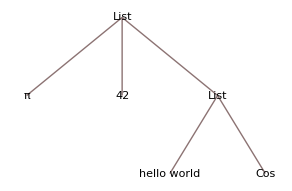

```mathematica
TreeForm[%%%]
```

These TreeForm expressions are still expressions. You can therefore, for example, make a list of them.

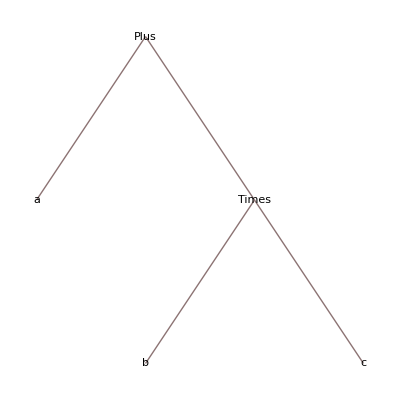
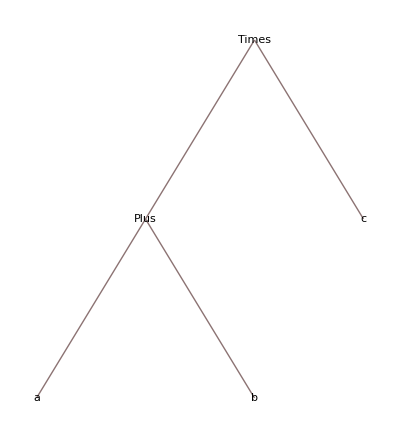
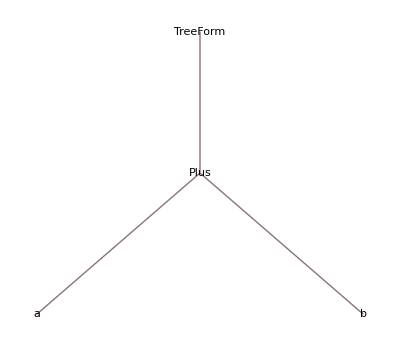

```mathematica
{ TreeForm[a+b*c], TreeForm[(a+b)*c], TreeForm[TreeForm[a+b]]}
```

The third expression in the above example is more important than it might initially seem. Since everything in Mathematica is a symbolic expression, applying TreeForm or N or any other such function always produces another expression. An expression has no way of escaping its expression-ness, no matter how you twist and turn it or what you try to prepend on it. This is all very Gödel, Escher, Bach to the extent that you would almost expect to see Achilles, Tortoise and the whole gang of friends to show up to philosophically ponder the meaning of all this. (Shouldn’t somebody eventually write that sequel at some point?)

Following the spirit of GEB and its strange loops where layers of abstractions end up chewing on their own tails, Mathematica can even talk about its own simplification process with the function Trace that can be applied to any expression, and produces the list of all intermediate expressions produced by the simplification steps. This can be an interesting way to explore the internal workings of Mathematica and illustrate the important lesson not just in computer science but in all life in general that most things that initially seem insurmountably complex will actually turn out surprisingly simple once you bother to crack them open. (On the other hand, many things that seem rather simple or even trivial, for example integers and their addition and multiplication, will often turn out to be surprisingly complex when cracked open the same way. Or trying to teach the computer to walk and chew bubblegum at the same time, since tasks that are simple for a four year old are extremely difficult for computers, and vice versa.)

```mathematica
Trace[Sum[(x-1)^i, {i, 1, k}]]
```

{∑_(i=1)^k (x-1)^i,{{x-1,-1+x},(-1+x)^i},∑_(i=1)^k (-1+x)^i,((-1+(-1+x)^k) (-1+x))/(-2+x)}

If you already realized that even Trace doesn’t take you out of the realm of expressions but that the result that it evaluates to is an expression that consists of a list of expressions, you are well on your way to one day joining the mythical order of Knights of the Lambda Calculus. (Only the members know that they are members.) Since Trace is itself a Mathematica function, tracing the simplification of expressions that are headed by it is absolutely no different from tracing any other expression.

```mathematica
Trace[Trace[Sum[(x-1)^i, {i, 1, k}]]]
```

{Trace[∑_(i=1)^k (x-1)^i],{∑_(i=1)^k (x-1)^i,{{x-1,-1+x},(-1+x)^i},∑_(i=1)^k (-1+x)^i,((-1+(-1+x)^k) (-1+x))/(-2+x)}}

In fact, the rule of everything being an expression extends to the notebooks themselves, which are just really long expressions that contain Cell expressions inside them. The Mathematica front end displays these notebooks and their cells in a graphical interactive form. (Perhaps Mathematica itself is also an expression that is eternally trying to simplify itself? And how about you, the dancing dust in the wind that will one day return to the same ground that it rose from?) We can ask Mathematica for the list of Notebook objects that are currently open, and then perform computations on these notebooks just like with any other expressions.

```mathematica
Notebooks[]
```

{a8x8t_shm105FrontEndObject[LinkObject["a8x8t_shm", 3, 1]]105expressions/Users/ilkkakokkarinen/Google Drive/Mathematica/expressions.nb,a8x8t_shm100FrontEndObject[LinkObject["a8x8t_shm", 3, 1]]100Satisfiability/Users/ilkkakokkarinen/Desktop/Ilkka/WolframExamples/Satisfiability.nb,a8x8t_shm81FrontEndObject[LinkObject["a8x8t_shm", 3, 1]]81SnakesAndLadders/Users/ilkkakokkarinen/Desktop/Ilkka/WolframExamples/SnakesAndLadders.nb,a8x8t_shm84FrontEndObject[LinkObject["a8x8t_shm", 3, 1]]84JavaExercises/Users/ilkkakokkarinen/Desktop/Ilkka/WolframExamples/JavaExercises.nb,a8x8t_shm1FrontEndObject[LinkObject["a8x8t_shm", 3, 1]]1Messages}

Mathematica differs from almost every other programming language in wide use today in that it has no formal typing. In strongly typed languages, integers, decimal numbers, strings, rectangles and bank accounts are all qualitively different things that are stored and processed differently within the language and its implementation.

In statically typed programming languages such as C and the myriad of languages that descended from it, this segregation is strictly enforced by the language so that whenever you wish to use some symbol, you have to declare it as an int or double or whatever else you want it to be, and from then on, you are allowed to use that variable to store only that type of data and nothing else. This restriction is enforced because it offers important advantages. First, it creates type safety against errors where you treat some data in a way that makes no sense for its type: for example, you try to divide the text string "Hello world" by the integer 7, an operation that is nonsense by definition and could only therefore crash your program if it were allowed to execute. The second advantage is the speed of the resulting executable program, since the execution environment does not have to be all the time checking what type something is and how it should therefore be handled. Dynamic languages such as Python and Ruby are not statically typed, but they are still typed (and even silently compiled before executing the script, even though most people don’t seem to realize this), so that, for example, the string “42” is not the same thing as the integer 42.

In Mathematica, everything is an expression, which is essentially the only "type" that the language contains, and each expression is simplified by the repeated application of built-in and user-defined patterns to the extent that it can be simplified. Expressions are, well, expressive enough to distinguish between various types of things such as points, bank accounts, plots and the monarchs of the ancient history that we may wish to represent in our programs. All distinctions between different "types" of expressions, whenever this turns out to be necessary, are made dynamically based on the Head of the expression. Whenever this distinction is not necessary, we can treat expressions as expressions, and therefore any function that we write is polymorphic, that is, can be used for very different types of data.

Even if an expression makes no sense for human or machine alike, it can still be a legal expression same way that the classic nonsensical natural language sentence “Colorless green ideas sleep furiously” is syntactically perfectly correct, but doesn’t mean anything.

```mathematica
"Hello world" / 7
```

(Hello world)/7

Even an outright nonsensical expression may allow further simplications after it is combined with something else.

```mathematica
% / "Hello world"
```

1/7

Pay attention to the important distinction between symbols and text strings. The symbol chain Hello world is not the same thing as the text string “Hello world”, the latter given between a pair of quote marks. The use-mention distinction exists in the programming languages exactly the way that it exists in natural languages, both being just froth on the surface of thought regardless of whether the language evolved naturally or was artificially constructed. (It remains to be seen whether somebody will ever come up with an esoteric programming language that requires the use of scare quotes or finger quotes!)

```mathematica
%% / (Hello world)
```

(Hello world)/(7 Hello world)

Internally, Mathematica stores all lists and expressions using a random access representation (usually called an array in imperative programming languages, but this should not be confused with Mathematica’s function Array and its relatives), which allows you to easily and efficiently pick an element at an arbitrary position of the list with the function Part, or its more common syntactic sugar shorthand notation [[idx]]. (Note that unlike most other programming languages, Mathematica list indexing requires the square brackets to be duplicated, because single square brackets are already in use to mean function application.) The result simplifies to the expression in that position of the list.

```mathematica
{Sin, Cos, Tan}[[RandomInteger[{1, 3}]]][x]
```

Cos[x]

If the index idx given between the double square brackets is a list of positions, the result is the list of elements in those positions.

```mathematica
{"One", "Two", "Three", "Four"}[[{1, 3}]]
```

{One,Three}

The distinction between random access and internal list representations is not really that important right now, but when doing more advanced work, it is important to understand why some simple modification of a list such as appending one element to the front actually necessitates creating a separate copy of the entire list for the result, since the old value must still exist for the computations that need it. This seems quite silly if the list has a million elements, and yet is necessary for the append to work correctly. However, it would be equally silly to maintain the list element data internally in a linked list representation and therefore make the function Part to have to walk from the start of the list to the given location one step at the time, instead of being able to jump there directly in one step using random access. In computer science, the choice of data structures in which the data is stored will necessarily make some operations efficient and some others inefficient, and the choice of the operations that we perform on that data must reflect that underlying reality.

Mathematical objects such as points and vectors of arbitrary length are represented in Mathematica as lists of their components. The indexing operation [[ idx ]] can then be used to extract individual components. For lists treated as vectors, the functions Inner and Cross compute the inner (also called “dot”) and cross products, respectively. The inner product projects the length of the first vector on to the second (therefore computing the dot product of some vector with itself gives you the square of its length), whereas the cross product produces a vector that points away from the plane defined by its two argument vectors, the sign of the result determined by the right hand rule, and the length of the result equal to the signed area of the parallelogram defined by the argument vectors. Slightly confusingly, the function Inner also takes as its first argument an arbitrary function that it wraps around each pair.

```mathematica
v1 = {2, 3, 4};
v2 = {-1, 5, 3};
Cross[v1, v2]
Inner[Identity[#]&, v1, v2]
```

{-11,-10,13}

9

The function Norm that computes the length of the vector can be given an optional second argument to tell which distance metric to use. If no such option is given, the default value 2 corresponds to ordinary Euclidean distance. As this argument approaches infinity, the closer the norm gets to the longest individual component of the argument vector. The distance metric using parameter one is known as taxicab geometry or Manhattan distance, analogolous to the distance between two points when you are allowed to move only horizontally or vertically in a grid, but not to other directions as the crow flies.

```mathematica
{Norm[v1], Norm[v1, 3], Norm[v1, Infinity]}
```

{√29,3^(2/3) 11^(1/3),4}

The function Apply can be used to change the head of an arbitrary expression. This function will come handy later in functions that first generate some list that is then turned into something else using Apply by changing its head from List to that something else. For example, changing the head of the expression List[1, 2, 3] to Plus turns it into the expression 1 + 2 + 3, which Mathematica then further simplifies to the literal expression 6.

```mathematica
Apply[Plus, {1,2,3}]
```

6

As you will learn, lists are how Mathematica represents most of the data that it operates on. During these lessons, we will encounter the vast array of functions of Mathematica that operate on lists. Here is a small taste.

```mathematica
MeanFilter[{1, 2, 3, 4, 5, 6, 7, 8}, 2]
```

{2,5/2,3,4,5,6,13/2,7}

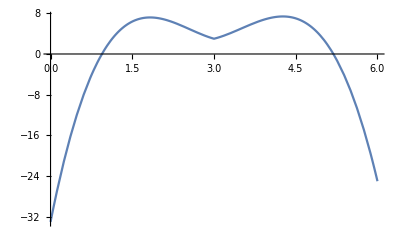

```mathematica
fi = ListInterpolation[{1, 7, 3, 7, 3}];
Quiet[Plot[fi[x], {x, 0, 6}]]
```

```mathematica
ContinuedFraction[π^π, 20]
```

{36,2,6,9,2,1,2,5,1,1,6,2,1,291,1,38,50,1,2,5}

```mathematica
FromContinuedFraction[%]
```

81086339098531/2223849052608

```mathematica
N[{π^π, %}, 30]
```

{36.4621596072079117709908260227,36.4621596072079117709908260641}

```mathematica
Convergents[π^π, 7]
```

{36,73/2,474/13,4339/119,9152/251,13491/370,36134/991}

```mathematica
N[%, 6]
```

{36.,36.5,36.4615,36.4622,36.4622,36.4622,36.4622}

Look up the list of all words in the English language that have the string “dog” somewhere in them, and check out a random sample of them. Then, use the function FindClusters to create list of clusters of similar words, and display the clusters in a Grid with each cluster in a framed column. The functions RandomSample and RandomChoice give you a random sample of the elements of the argument list, the first one choosing without replacement, the second one with replacement.

```mathematica
dogwords = DictionaryLookup[___ ~~"dog" ~~ ___];
RandomSample[dogwords, 10]
```

{dogsbodies,hangdog,bulldog,dogcatcher,doggies,dogleg,dogmas,dogtrotting,dogmatics,dogfought}

```mathematica
clusters = FindClusters[dogwords, 20];
Grid[Partition[Map[Framed[Column[#]]&, clusters], 5]]
```

boondoggle
boondoggled
boondoggler
boondogglers
boondoggles
boondoggling | bulldog
dog
lapdog
underdog | bulldogged
dogged
doggedly
doggerel
doggy
doglegged
dogsbody
dogsled
dogsleds
dogwood | bulldogging
doggier
doggies
doggiest
dogging
dogies
dogsbodies | bulldogs
hotdog
hotdogs
lapdogs
sheepdogs
underdogs
watchdogs
dogcart
dogcarts | dogcatcher
dogcatchers | doge
doges
dogs
endogenous | dogeared | dogfight
dogfighting
dogfights
dogfish
dogfought
dogfishes | doggedness
doggone
doggoned
doggoner
doggones
doggonest
dogwoods | doggoning
doglegging | doghouse
doghouses
endogenously | dogie
dogleg
doglegs | dogma
dogmas
Ladoga | dogmatic
dogmatically
dogmatics
dogmatism
dogmatist
dogmatists | dogtrot
dogtrots
dogtrotted
dogtrotting | hangdog
sheepdog
watchdog

## Substitutions and rules

Substitutions are the second important subtype of expressions that we need to know to advance in Mathematica programming. Syntactically, a substitution rule consists of two expressions separated by the right arrow character. Substitution rules don’t do anything by themselves, but their purpose is that they can be applied to arbitrary expressions using the slashdot operator that has the effect of replacing every occurrence of the substitution rule’s left hand side in that expression with their right hand side. If the left hand side of some rule doesn’t occur anywhere in the expression, that rule has no effect and nothing happens.

```mathematica
{a, a+1, a+2, a+3} /. a-> (x+y)
```

{x+y,1+x+y,2+x+y,3+x+y}

```mathematica
% /. x-> 7
```

{7+y,8+y,9+y,10+y}

Matching of the substitution is rule takes place in the expression tree structure, not in its linear textual representation that really exists only for the convenience of the human reader. Even when the textual representation seemingly contains a match for the left hand side of the substitution rule, the substitution cannot operate when the match is split between separate parts of the expression tree.

```mathematica
a *b + c * d /. b + c -> 99
a*(b+c) * d /. b+c -> 99
```

a b+c d

99 a d

If the slashdot operator is given a list of substitution rules, it will try to apply them all.

```mathematica
(a+b) / (c / d) /. {a->3, c -> -5, x -> 42}
```

-1/5 (3+b) d

If the slashdot operator is given a list of lists of substitution rules, the result is the list of applying each list of rules individually.

```mathematica
(x+y) /. { {x->2, y->3}, {x-> 1}, {y-> f[α, β]} }
```

{5,1+y,x+f[α,β]}

For reasons of both efficiency and effective computability, the substitution always requires the match to be structurally exact, and it doesn’t try to twist and turn each argument expression every possible way to find out if the substitution could be performed after the expression has been converted to some equivalent but more amenable form.

```mathematica
x^4 /. x^2 -> hop
```

x^4

I see... but this will probably work, then?

```mathematica
(x^2)^2 /. x^2 -> hop
```

x^4

Nope. When Mathematica simplifies this given expression, the expression that resides before substitution gets simplified as much as possible before the substitution is even attempted. The special form Hold can be used to prevent Mathematica from simplifying the expression, forcing it to maintain it exactly as it was given. However, substitutions can still be performed in an expression that has been frozen with hold. The hold keeps holding until ReleaseHold is explicitly used to release it.

```mathematica
ReleaseHold[Hold[(x^2)^2] /. x^2 -> hop]
```

hop^2

Notice in the above example that the substitution must be placed outside the parentheses bounds of Hold, since otherwise it would be part of the Hold and would not be applied either, so after the ReleaseHold, we would just end up back where we started. The slashdot operator is able to perform some manipulations trying to find a match, though. For example, symmetric operators such as Plus are tried both ways, if a match is not found otherwise.

```mathematica
x + y /. y + x -> 7
```

7

The slashdot operator performs the substitution only once. Its variation slashslashdot keeps applying the substitution as long as it matches something, no matter how many times this happens. This operation is therefore somewhat dangerous in that it can easily get stuck in an infinite loop. (If you get stuck in an infinite loop, you can force it to quite by selecting “Abort Evaluation” in the Evaluation menu.) Alternatively, when using the function ReplaceRepeated instead of its syntactic sugar shorthand, the function can be given an option MaxIterations to constrain how many times it will perform the substitution before giving up.

```mathematica
ReplaceRepeated[1/x, x->1/(1 + x), MaxIterations -> 5]
```

ReplaceRepeated::rrlim: Exiting after 1/x scanned 5 times.

1+1/(1+1/(1+1/(1+1/(1+x))))

Substitutions can be used to “evaluate” a symbolic expression produced by some computation by substituting an actual value in place of the unbound symbolic variable. Note that Mathematica will always internally rearrange the operands of the function Plus so that the individual terms are listed in the ascending degrees of terms, the opposite of how we normally write out polynomials, and the terms of equal degree are listed in the alphabetical order.

The default behaviour of the right arrow operator in the substitution rule is eager; Mathematica first simplifies the substitution rule itself before using it in substitutions. This order might not be how you want this to go, especially in situations where the substitution rule should produce a different value at different times. For example, when use the function RandomReal as part of a substitution rule, you might want it to produce a new random number every time this rule is used. An alternative lazy version of the substitution arrow, denoted by :> instead of ->, keeps the substitution rule on hold, releasing the hold to simplify it again each time the substitution rule is applied. Of course, this would be rather inefficient if we know that the rule always produces the same result that would then be evaluated needlessly over and over again.

```mathematica
{x, x, x} /. x-> RandomReal[]
```

{0.907203,0.907203,0.907203}

```mathematica
{x, x, x} /. x :> RandomReal[]
```

{0.59758,0.929557,0.472029}

For now, we will use only simple unconditional substitutions, but the underlying machinery of patterns in substitution rules makes this mechanism far more powerful in that we could, in fact, use it to express arbitrarily complicated computations. We will return to this topic in a future lesson.

Armed with lists and substitutions, we can start using Mathematica’s massive knowledge base about formulas to solve equations and systems of equations and inequalities with almost arbitrary constraints of equalities and inequalities. The general purpose function Solve produces a list of substitutions for the solutions that it finds for your equations. Note that to express the constraint of mathematical equality, you need to duplicate the equals sign, since the single equals sign will unfortunately mean the eager assignment. First, we use Solve to find all three solution of a cubic equation for the unknown variable x. The function Solve always returns a list of solutions, even when the equation has only one solution. The empty list will then denote a set of equations that has no solutions.

```mathematica
Solve[x^3 - 4 x + 7 == 0, x]
```

{{x→-4 (2/(3 (63-√3201)))^(1/3)-(1/2 (63-√3201))^(1/3)/3^(2/3)},{x→2 (1+ⅈ √3) (2/(3 (63-√3201)))^(1/3)+((1-ⅈ √3) (1/2 (63-√3201))^(1/3))/(2 3^(2/3))},{x→2 (1-ⅈ √3) (2/(3 (63-√3201)))^(1/3)+((1+ⅈ √3) (1/2 (63-√3201))^(1/3))/(2 3^(2/3))}}

Let us verify the result by performing these substitutions to the original equation and see that the result is nothing but a list of three zeroes...

```mathematica
x^3 - 4 x + 7 /. %
```

{7-4 (-4 (2/(3 (63-√3201)))^(1/3)-(1/2 (63-√3201))^(1/3)/3^(2/3))+(-4 (2/(3 (63-√3201)))^(1/3)-(1/2 (63-√3201))^(1/3)/3^(2/3))^3,7-4 (2 (1+ⅈ √3) (2/(3 (63-√3201)))^(1/3)+((1-ⅈ √3) (1/2 (63-√3201))^(1/3))/(2 3^(2/3)))+(2 (1+ⅈ √3) (2/(3 (63-√3201)))^(1/3)+((1-ⅈ √3) (1/2 (63-√3201))^(1/3))/(2 3^(2/3)))^3,7-4 (2 (1-ⅈ √3) (2/(3 (63-√3201)))^(1/3)+((1+ⅈ √3) (1/2 (63-√3201))^(1/3))/(2 3^(2/3)))+(2 (1-ⅈ √3) (2/(3 (63-√3201)))^(1/3)+((1+ⅈ √3) (1/2 (63-√3201))^(1/3))/(2 3^(2/3)))^3}

Whoa, not quite! What is going on here? The reason behind this mess is that for efficiency reasons, the Mathematica simplification mechanism for mathematical formulas doesn’t attempt to follow every possible substitution rule sequence that it knows. To force Mathematica to do all it can to boil the result down to its bare bones, use the function FullSimplify. This will produce the best effort equivalent expression that Mathematica is able to find from its knowledge base chock full of all kinds of mathematical axioms and theorems.

```mathematica
FullSimplify[%]
```

{0,0,0}

We can sigh in relief; the invisible machinery of mathematics underneath this all has not stopped working. Saved by the bell, we can next do some implicit differentiation with an example equation taken from the textbook “Elementary Calculus” by H. Jerome Keisler. Without solving for y explicitly, calculate the value of the differential y’[x] in the point (√2, 1) that the little bird told us lies on the following implicit curve. Note how the function Solve can solve an equation with respect to arbitrary expressions, not just individual variables, and these expressions may even contain differentials of functions and many special functions. Before the equations, a small taste of Mathematica’s plotting capabilities and the function Show that can combine any numbers of plots and other graphics into one graphic.

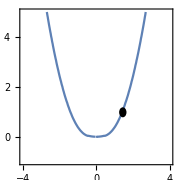

```mathematica
Show[ContourPlot[y + Sqrt[y] == x^2, {x, -4, 4}, {y, -1, 5}, AspectRatio -> Automatic], Graphics[Disk[{Sqrt[2], 1}, .2]], ImageSize -> Small]
```

In implicit differentiation, we first differentiate the function, producing a messy formula that we simplify by making Dt[x] to equals 1. Solving the rest for Dt[y] gives us a formula in which we can substitute any values of x and y, so let us substitute the point (√2, 1) that we are interested in.

```mathematica
Dt[y + Sqrt[y] == x^2];
%/. Dt[x] -> 1;
Dt[y] /. Solve[%, Dt[y]];
First[%]/. {x->Sqrt[2], y-> 1}
```

(4 √2)/3

The functions Maximize and Minimize can find symbolic maximums and minimums for functions that contain variables with arbitrary constraints. The answer to the classic high school math problem of maximizing the volume of a box when the sum of the three side lengths can be at most 10 turns out to be the cube. In defining the constraint as a single formula, the symbol ∧ is used to denote conjunction.

```mathematica
Maximize[{a * b * (10-a-b), 0 < a ∧ 0 < b ∧ a + b ≤ 10}, {a, b}]
```

{1000/27,{a→10/3,b→10/3}}

What about minimizing the volume of a cylinder where the radius and height each have to be at least one, and their sum must be exactly equal to 10? There is a problem we would find in a high school calculus final exam. Since increasing the radius increases the total volume more than would increasing the height by the same amount, the optimal solution makes the height as large as possible while keeping the radius at minimum.

```mathematica
Minimize[{Volume[Cylinder[{{0, 0, 0}, {0, 0, h}}, r] ] , 1 <= r ∧ 1 <= h ∧ r+h == 10},{r, h}]
N[%, 5]
```

{9 π,{r→1,h→9}}

{28.274,{r→1.,h→9.}}

What exactly constitutes the "simplest" equivalent expression inside the function FullSimplify is determined by the ComplexityFunction that is given as an optional argument to the function FullSimplify. In principle, this function could be any cost function whatsoever, no matter how wacky, but most of the time, it will be one of the predefined cost functions of Mathematica. The built-in cost function LeafCount counts only the number of subexpressions, regardless of how long these subexpressions happen to be. In absense of an explicit cost function, the default one used by FullSimplify simply adds up the number of subexpressions and the digits in integer literals.

```mathematica
FullSimplify[1000Log[2], ComplexityFunction -> LeafCount]
```

Log[10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376]

```mathematica
FullSimplify[1000Log[2]]
```

1000 Log[2]

Everyone remembers sitting in the math class solving equations by hand and having to be careful not to slip and make mistakes, silently thinking that there ought to be a way for steam power to somehow automatically slough through this drudgery by making these calculations for you. Today, this dream of Charles Babbage is finally reality in our fingertips. The vast equation churning machinery hidden under the hood of the simple-to-use function Solve works for, within the natural limitations of the underlying machine and amount of execution time, any number of unknowns and constraints. For more than one equation, the first argument must be a list of equations, while the second argument must be a list of the unknowns of these equations whose values you want to solve. The result is a list of lists of substitutions for the variables that solves the equation.

```mathematica
Solve[{x+y == a, 2 x^2 - 7y == b}, {x, y}]
```

{{x→1/4 (-7-√(49+56 a+8 b)),y→7/4+a+1/4 √(49+56 a+8 b)},{x→1/4 (-7+√(49+56 a+8 b)),y→1/4 (7+4 a-√(49+56 a+8 b))}}

Again, we use substitution to verify the correctness of the solution.

```mathematica
FullSimplify[{x + y == a, 2x^2 - 7 y == b} /. %]
```

{{True,True},{True,True}}

The truth values True and False are symbols in Mathematica that equations and other expressions can simplify to, just like they can simplify to numbers and other expressions.

```mathematica
2 + 2 == 4
```

True

```mathematica
E^(I π) + 1 == 0
```

True

```mathematica
ForAll[x, x^2 ≥ 1]
```

∀_x x^2≥1

```mathematica
Resolve[%, x ∈ Reals]
```

False

```mathematica
π ∈ Algebraics
```

False

The reason that equality comparison is syntactically expressed using the duplicated equals sign, going against the convention used in mathematics everywhere from elementary schools to the chambers of the highest ivory tower, is that unfortunately even the designers of Mathematica were not able to escape the firmly rooted convention of programming language syntax that a single equals sign symbol = is used for assignments where some symbol is given a definition to be used in its place whenever it occurs in the future.

Mathematica even features a triple equals sign for checking if two expressions are structurally identical. This is a stronger property than equality in the sense of == that both expressions simplify to the same result. Just like in life in general, where equality allows freedom to enter, inequality will quickly slip in in its wake.

```mathematica
1 === Sin[x]^2 + Cos[x]^2
```

False

```mathematica
FullSimplify[Sin[x]^2 + Cos[x]^2]
```

1

The operator === is a syntactic sugar shorthand for the function SameQ to test for structural equality. This function name illustrates the naming convention for Mathematica built-in functions that query whether something is True or False by naming such functions with the suffix Q. This convention itself is a relic from a more primitive era when the programming languages, including Mathematica, reflected the fact that only Western characters were included in the character sets handled by computers, and only letters and numbers were allowed in the names of variables and other symbols. These functions would be better named with a trailing question mark in style of Same? and so on. However, since the language has to remain backwards compatible so that all Mathematica code written in the older versions in the language will continue to work exactly the same now and in the future as it did back in the day that it was originally written, it is not possible to now change the names of these functions to something more expressive. In not just computer science but in all engineering in general, the design decisions that we do today to simplify our current tasks can stick on to keep on keeping on far longer in the future than anybody could have expected. (The engineering folklore story of how the width of the U.S. standard railroad gauge ultimately derives from the width of the war chariots of the Imperial Rome is still only an urban legend, though.)

To spice up the next examples, so far we have used only ordinary lowercase Western characters as symbols, but there are plenty of other symbols available, so we can make out Mathematica programs look more like formulas that you would find in a mathematics textbook. Greek letters are easy to type in as their names between two presses of the Escape key.

```mathematica
α = 7;
β = α + 5;
{ α * 2, β}
```

{14,12}

The assignment operator is eager so that Mathematica will simplify the right hand side expression before assigning it to the left hand side symbol. If that expression simplifies to a single numerical literal value, then, well, that is what that expression simplifies to. The symbol β is now associated with the value 12 instead of the expression α + 5 that originally produced that value. Mathematica is not a spreadsheet, so changing α later to something else has no effect on the value of β .

```mathematica
α = 2;
β
```

12

To get the behaviour that we wanted here, the operator := is the lazy version of assignment that holds the right hand side expression in unevaluated form, and evaluates it again every time that its left hand side is used somewhere.

```mathematica
γ := 7;
δ := γ + 5;
{ γ * 2, δ }
```

{14,12}

```mathematica
γ = 2;
δ
```

7

Same as with the eager and lazy versions of the substitution operator, the eager and lazy assignment behave differently in situations where the value of the right hand side expression is a fluent that changes over time. Typical example of this situation would again be the various random number generation functions. (Strictly speaking, these symbols are not functions in the mathematical sense, since they return a different answer every time they are called for same arguments.)

```mathematica
n1 = RandomReal[];
n2 := RandomReal[];
{n1, n1,n1,n1}
{n2, n2,n2,n2}
```

{0.740107,0.740107,0.740107,0.740107}

{0.269142,0.956755,0.657307,0.80954}

The deterministic computer processor cannot by itself produce any random quantities. Under the hood, all random number generator functions have an internal invisible parameter, the current state of the random number generator, and the result is deterministically determined by the generator’s current state. You can set the generator state with the function SeedRandom, and then try generating a couple of random numbers to verify that you indeed get the same answers every time. The function built inside the generator is chaotic in the sense of being highly sensitive to small differences in the initial state; changing the seed just a little bit will soon enough make the resulting series of numbers completely different. The term pseudorandom numbers is used to refer to such numbers that are in principle fully deterministic, but sufficiently chaotic and unpredictable for our purposes that they are as good as random.

```mathematica
SeedRandom[123456];
RandomInteger[{1,100}, 20]
```

{63,46,98,47,96,12,5,45,43,29,17,100,34,73,93,45,86,71,87,13}

```mathematica
SeedRandom[123456];
RandomInteger[{1,100}, 20]
```

{63,46,98,47,96,12,5,45,43,29,17,100,34,73,93,45,86,71,87,13}

```mathematica
SeedRandom[123457];
RandomInteger[{1,100}, 20]
```

{8,82,57,36,58,34,51,2,94,72,66,82,26,56,38,48,90,17,30,60}

Finally, you can perform multiple assignments in one swoop by assigning the list on the right hand side to a list of symbols. Mathematica will match the parts of the right hand side to the corresponding parts of the left hand side. This works only for lists, so you can’t unify two arbitrary expressions the way you could in the logic programming language Prolog.

```mathematica
{jack, rick, nick } = {4, x+y, "hello"};
rick + nick
```

hello+x+y

```mathematica
bob + carol = ted + alice
```

Set::write: Tag Plus in bob + carol is Protected.

alice+ted

## Functions

After lists and substitution rules, functions are the last special type of expressions that we need to have to access the full power of programs written in Mathematica. Functions are expressions that can be applied to other expressions using the syntax f[x], where the square brackets are required to indicate that you are applying the function f to its argument x. (As we said earlier, ordinary parentheses are used for expression grouping, so they cannot be used around function arguments.) Simplifying this expression produces the expression that is the result of this function. Until you get accustomed with the square brackets, you will often find yourself writing the function calls using ordinary parentheses, but the cold unflinching eye of TreeForm shows the result of that mistake.

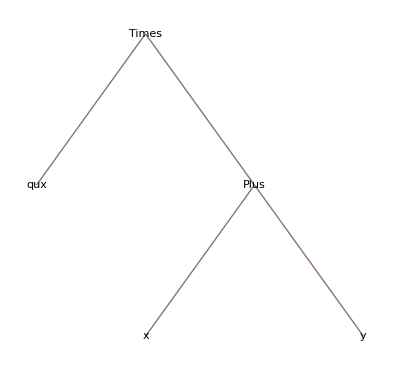
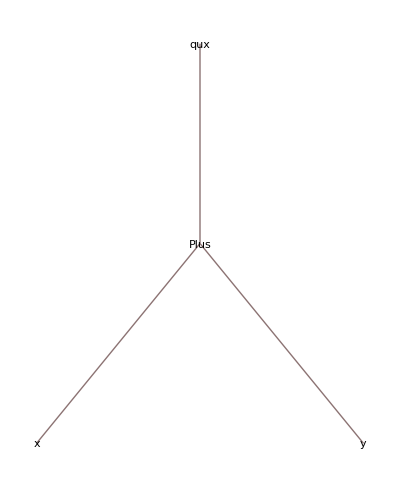

```mathematica
{qux(x+y) // TreeForm, qux[x+y] // TreeForm}
```

In most programming languages, the separation of code and data is strictly enforced so that the functions written in those languages are a qualitatively different thing from numbers, text string and other data objects that those functions operate on. In imperative programming, code is set in stone in compilation and cannot be changed afterwards while it is being executed, whereas data lives dynamically during the program execution so that every value can be freely changed to something else, the memory are of values evolving from inputs to the resulting outputs one step at a time. No such distinction of code and data exists in Mathematica at all since the language is homoiconic, meaning that both the functions and the data that they operate on are the exact same kind of symbolic expressions. Code is data, and data is code, both interchangeable when needed.

In Mathematica, there exists nothing but symbolic expressions and their simplification rules. Nothing else. Ever. Sometimes we choose to display these symbolic expressions in different ways using the Mathematica front end. Some of these ways and some expressions end up looking more flashy and graphical than others, but the expressions themselves will always remain just that, expressions, independent of how we happen to view and think about them.

The first, and the most explicit and verbose, way to define a function is to use the second-order function Function that takes two parameters. The first parameter specifies the arity and the names of the parameters expected by the function that is being defined. (If there are two or more parameters, you need to give these parameter names as a list.) The second parameter, the function body, then describes what the function actually does with the arguments that it receives. The function defined this way can then be applied to arbitrary argument expressions, just like any other function that is already built in the system. In the next two expressions, the ordinary parentheses around the Function are not necessary, but are used here to make it clearer that a function produced by the Function expression is applied to the arguments that follow in square brackets.

```mathematica
(Function[x, x^5])[a+b+7]
```

(7+a+b)^5

```mathematica
(Function[{x, y}, Sqrt[{x^2 + y^2}]])[3, 2]
```

{√13}

Functions are symbolic expressions that can be assigned to symbols no different from any other symbolic expressions. So that you don’t need to always retype the same function every time you want to use it, you should assign it to some conveniently named symbol, and then use that symbol as the function name to invoke it for arbitrary arguments.

```mathematica
f := Function[x, 3*x + 1];
f[7]
```

22

The next syntactic shorthand will certainly take some time to get accustomed to, but it occurs so often in other people’s code and the examples in the rest of the lessons that it must be shown here for that reason. Instead of using Function to define a function, when tacked on the end of an arbitrary expression, the operator & does the same thing by creating a pure function. Since there is no place to indicate which symbols are arguments and which are merely other symbols, the special symbol # is used as a placeholder for each argument so that in the function body, #1 (or just #) means the first argument, #2 means the second argument, #3 the third, and so on. For example, a function that takes two parameters and produces the square root of the sum of their squares.

```mathematica
((Sqrt[#1^2 + #2^2])&)[3, 2]
```

√13

This pure function notation (or using the terminology more common in other programming languages, an anonymous function) will be often used in later lessons to create some little bitty function on the fly to be passed as an argument to another function that then uses it to do something. The functions that you define yourself are no different from those functions that already exist in Mathematica. You can pass your functions as arguments to metafunctions, that is, functions that operate on other functions the same way that ordinary functions operate on integers, real numbers, lists, klotzbloms and other things. (The concept of a “metafunction” exists here merely for our convenience, since all functions in Mathematica operate on arbitrary expressions, and produce expressions as their results when they are evaluated by simplification. The distinction between functions, lists, substitutions and other subtypes of expressions is just for our convenience... and sometimes for inconvenience.)

```mathematica
Solve[f[x] == 7, x]
```

{{x→2}}

```mathematica
Sum[f[i], {i, 1, k}]
```

1/2 (5 k+3 k^2)

If the function is long and complicated, we often want to use local variables inside its body to store the intermediate results that it needs along the way so that these local variables will not accidentally conflict with any global symbol definitions that we have done earlier. In Mathematica, the function Module is used to define a local computation context so that the symbols defined in it are quietly renamed with a prefix that guarantees that they cannot conflict with the names defined outside this context. The next piece of code shows the difference between a globally defined symbol a, versus a local definition of a that exists only inside the Module that is inside the definition of an anonymous function. The Mathematica front end will helpfully distinguish between global and local definitions by using different colours to highlight the symbols.

```mathematica
a = 42;
f := (Module[{a = 5}, #+a])&;
{a, f[5], a, f[10]}
```

{42,10,42,15}

Modules are still expressions, albeit more complicated than those that we have seen before, so they can be assigned to variables and be subexpressions of lists and other expressions. Other than the limited memory of the physical computer that executes Mathematica, there is no limit how deep this nesting of modules could go, as illustrated in the next example. Even using the exact same symbol in several nested modules is perfectly legal but still hinky and therefore not recommended, so Mathematica tries to not-so-subtly draw our attention to it with the alarming red colour, even though it will still obediently simplify the compound formula when we tell it to do so. The function Print is used to output the current value of an expression, as if we had suddenly found ourselves dropped inside C, Pascal, Basic or some other old school imperative programming language. (In these sorts of hinky situations, serious compilers of such languages would issue a warning about your program.)

```mathematica
b = 17;
Module[{b = 42},
Module[{b = 99},
Print[b];
];
Print[b];
];
Print[b];
```

99

42

17

Since pure functions are expressions, and functions produce expressions when they are applied to their arguments, we can write functions that return functionsas their results. Once the function produces another function as the result, that result function is a closure that still remembers the definitions made in the local context of the original function. The classic functional programming example of writing an accumulator is a common textbook example of this technique. You should examine the next example carefully; the symbol accum is assigned to be a pure function that takes no parameters and creates and returns a pure function that increments the local variable value by its parameter each time, returning the new value. We call the function accum once, and assign the anonymous function that it produces to the symbol a so that we are able to talk about something that itself has no name. This symbol a is then used to call that anonymous function four times. It seems that Mathematica evaluates the elements of a list from left to right.

```mathematica
accum:= (Module[{value},value = #;(value = value  + #)&])&;
a = accum[10];
{a[3],a[5], a[2], a[-10]}
```

{13,18,20,10}

Calling accum again gives us another anonymous function that we assign to another symbol b. This function is a separate expression from the one that we previously assigned to the symbol a, and therefore has a separate internal state and computation context. Mathematica keeps each module and its computation context around in the kernel memory as long as some active expression is still potentially using it.

```mathematica
b = accum[1000000];
{b[1], b[3], a[1], b[5]}
```

{1000001,1000004,11,1000009}

That is it for functions defined with Function and the anonymous function syntax. An alternative way, in practice far more common, to define functions is to use patterns in an assignment, as seen in the example below. The underscore in the parameter name on the left hand side of the definition serves as a placeholder that can match any expression whatsoever. This underscore is necessary for the function to work as we intended. If you leave it out, you define the function g only for the exact literal symbol t, instead of defining it for any expression whatsoever, for which the symbol t is used as a placeholder name in the function body. In the function body on the right hand side, you should not use the underscore, but just the parameter name without it. For example, define a function g[t] and plot its trigonometric glory.

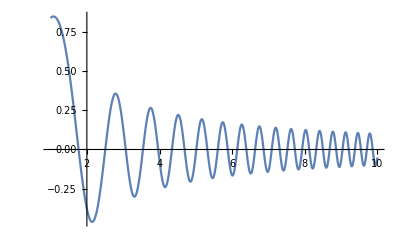

```mathematica
g[t_] = Sin[t^2]/t;
Plot[g[t], {t, 1, 10}]
```

## Graphical plots of functions

Patterns and their matching are a very powerful tool to define computations, and we will expand upon them in a later lesson. Before that, now that we just popped off the cap off that pen, now would be a good time to take a look of Mathematica’s powerful built-in function plotting capabilities. The function Plot produces a graphical plot of the function (or a list of functions) that you give it over the range of values for its parameters. If you check out Plot in the Mathematica online documentation, you get the list of the myriad optional settings and other tweaks that allow you to adjust the style of the plot. However, the central design principle behind Mathematica is that every built-in function has a reasonable default behaviour that does what you want and works well with other parts of the language, so usually you don’t need to twiddle with these optional parameters at all. For example, plotting multiple functions in the same plot already knows to give each curve a different colour.

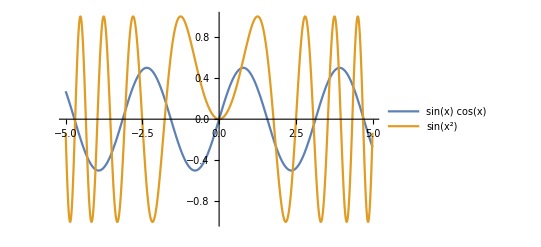

```mathematica
Plot[{Sin[x]Cos[x], Sin[x^2]}, {x, -5, 5}, PlotLegends -> "Expressions"]
```

Plots and other graphics are not exempt from the rule that everything in Mathematica is a symbolic expression. The Mathematica front end will just happen to display these graphics, well, graphically, instead of the boring way as a textual symbolic expressions that would make little sense for the human reader. But we know these expressions are there under the hood, and can see the full form any time we wish When the expression is huge, the Mathematica front end shortens up its presentation.

```mathematica
FullForm[%]
```

Legended[Graphics[List[List[List[],List[],List[1],List[Directive[Opacity[1.],RGBColor[0.880722,0.611041,0.142051],AbsoluteThickness[1.6]],Line[List[List[-5.,-0.132354],List[-4.99693,-0.162677],1480,List[5.,-0.132354]]]]]],List[1]],1]
 |  |  |  |

Here is another plot, demonstrating the optional Filling setting of Plot and how Mathematica will automatically use different colours and opacity to render multiple functions.

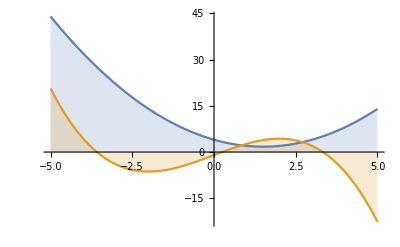

```mathematica
Plot[{x^2 - 3x + 4, -x^3/3 + 4x -1}, {x, -5, 5}, Filling -> Axis]
```

To visualize functions that take two parameters, you can use Plot3D to produce a three-dimensional heightfield. Strictly speaking, since your screen is still only two-dimensional pixel grid, what you really get from this function is a two-dimensional perspective projection of this three-dimensional heightfield. Furthermore, the rendering mechanism uses colour and lighting cues to guide the benevolent human viewer to visualize the underlying three-dimensional object from its two-dimensional image. The plot that is rendered is not just a simple pixel raster, but a symbolic expression that remembers what data originally produced it, and thus allows the same plot to be later rendered in other ways. For example, in a Mathematica notebook you can grab any three-dimensional image and rotate it with the mouse to inspect its contents from other, more convenient directions. Once the document is converted to PDF or some other non-Mathematica format, it becomes pure vector graphics and is no longer a live symbolic computation that you could freely rotate and adjust.

```mathematica
wavy = Function[{x,y},Sin[y]Cos[x]Sin[x^2]Cos[y^2]];
Plot3D[wavy[x,y], {x, -10, +10}, {y, -10, +10}, Mesh-> None, ColorFunction -> Function[{x, y, z}, Hue[x+y+z]]]
```

-Graphics3D-

Alternatively, you can plot two-dimensional data either as a DensityPlot or a ContourPlot, using colour to illustrate the values and the way that they change.

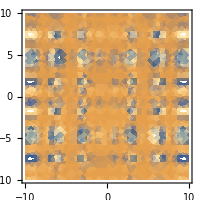

```mathematica
dp = DensityPlot[wavy[x,y], {x, -10, +10}, {y, -10, +10}];
Show[dp, ImageSize -> {200, 200}]
```

```mathematica
cp = ContourPlot[wavy[x,y], {x, -10, +10}, {y, -10, +10}];
Show[cp, ImageSize -> {200, 200}]
```

-Graphics-

ContourPlot can also be used to visually “solve” some equation by plotting only some particular contour lines.

```mathematica
cp2 = ContourPlot[wavy[x,y] == 2, {x, -10, +10}, {y, -10, +10}];
Show[cp2, ImageSize -> {200, 200}]
```

-Graphics-

The function Show can combine existing plots and other Graphics objects into a single Graphics object. Even if you don’t know Lena, surely you must have already seen her somewhere in the Internet, sometimes accompanied with her old friend the Mandrill. (Perhaps these two could be the visiting characters in that GEB sequel. The dialogue between them about existing simultaneously in different planes of meaning and existence would practically write itself.)

```mathematica
lena = RangeFilter[ExampleData[{"TestImage","Lena"}], 5];
Show[dp, cp2, Graphics[Inset[lena, {4, 4}], Opacity[0.5]], ImageSize -> {300, 300}]
```

-Graphics-

For continuous functions, Plot and Plot3D create a continuous plot, sampling for values until the desired precision of the result has been reached. DiscretePlot and DiscretePlot3D sample the functions at a predefined set of discrete values.

```mathematica
DiscretePlot3D[wavy[x,y], {x,-10, 10, 1}, {y, -10, 10, 1}, ExtentSize -> 0.5, ImageSize -> Medium]
```

-Graphics3D-

Ordinary plots display a function that is evaluated through the ranges of x- or y-coordinates. Parametric plots display some parametric curve that snakes through the space by evaluating the functions that produce the x- and y-coordinates through the ranges of parameter variables, which are usually canonically named with letters s, t or u. Unlike an ordinary plot that iterates through the range in linear order producing only one y-coordinate for each x-coordinate value, a parametric plot can zig and zag back and forth as you please.

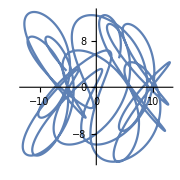

```mathematica
x[t_] := 9 Sin[t/17] + 4Cos[t/3];
y[t_] := 5 Cos[t/13] + 8Sin[t/4];
ParametricPlot[{x[t], y[t]}, {t, 0, 100π}, ImageSize -> Small]
```

The next example adds a third dimension to the mix. If you increased the range of the parameter variable t enough, the squiggly curve would eventually return to the point that it started from. The value of t needed to achieve this depends on the coefficients of the terms before and inside the trigonometric functions, and is here so large that the plot would become quite thick and messy.

```mathematica
z[t_] := 10 Cos[t/10];
ParametricPlot3D[{x[t], y[t], z[t]}, {t, 0, 100π}, ImageSize -> Medium]
```

-Graphics3D-

When you define symbols using the assignment operator, you are giving these symbols downvalues. These are the expressions that Mathematica associates to your symbol in its internal knowledge base of symbolic mathematics.

```mathematica
DownValues[z]
```

{HoldPattern[z[t_]]:>10 Cos[t/10]}

The earlier parametric plots seemed a bit messy, so we would prefer to render something more symmetric and aesthetically pleasing. Let us plot a connected chain of epicycloids so that each epicycloid consists of a point that revolves in a circle around the previous point using the fixed radius r, angular velocity τ and initial angle ϕ. The function epic[i, t] below gets two parameters so that i is the index of the epicycloid in the chain, and t is the current time. The function returns a point that the point i is at time t, given as a list of two elements that are the x- and y-coordinates of the curve at time t.

A connected chain of epicycloids is a good example of something that is self-similar. Seen the first time, this term might seem rather silly, since isn’t everything by definition not just similar but identical to itself? Indeed it is, but this term refers to a thing that is similar to some smaller part of itself. Recursion, the technique of defining something by means of smaller copies itself, is a handy technique to model self-similar phenomena and with some practice becomes almost automatic, the only difficulty lying in spotting the self-similarity after which it is all just mechanics.

The function epic is defined recursively so that the point 0 remains stationary at the origin, serving as the base case of this recursion. A base case means that the problem is so simple that we know the answer on the spot without any recursive computations. (Every recursion must have at least one base case so that it doesn’t end up being “turtles all the way down”.) The position of each point i + 1 is then computed from adding the components of the current radius vector, directed to the current angle of the point, to those of the recursively computed position of the previous point i. The function If is used to check whether we are in the base case. This function takes three arguments, the condition and two expressions. The simplification of If starts by evaluating its condition, and then exactly one of the following expressions is evaluated depending on whether the condition is true or false.

```mathematica
τ = {-.2, 0.5, 1.2, -7.8};
r = {2, 1, 1/2, 1/7};
ϕ0 = {0, 0, 0, 0};
epic[i_, t_] := If[i > 0,
epic[i-1, t]+ r[[i]]{ Cos[ϕ0[[i]] + τ[[i]] * t], Sin[ϕ0[[i]] + τ[[i]] * t]}
,
{0, 0}
];
```

To show what this function does, let us create a Table of five parametric plots, one for each of the points from zero to four, and then superimpose all these plots into a single plot using the function Show that is able to combine any kind of Graphics objects into one graphic. The resulting superimposition plot displays the trajectories of all five points. Note the base case point zero that remains stationary at the origin, and the point one that revolves around point zero in a simple circle. The higher-index points display more varied and interesting behaviour. You can try modifying the angular velocities and radii given in the lists τ and r and observe the effect of these parameters to the result.

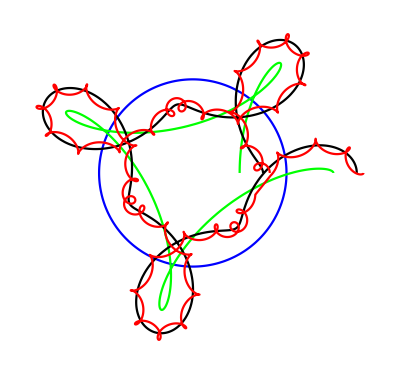

```mathematica
Show[Table[ParametricPlot[epic[i, t], {t, 0, 10π}, PlotRange-> All, Axes-> False, PlotStyle -> {Black, Blue, Green, Black, Red}[[i+1]]], {i, 0, 4}]]
```

I will never grow tired of pointing out that all evaluation of expression in Mathematica is fully symbolic. Unlike in all those primitive imperative languages, the previous function can be partially evaluated using symbolic arguments, requiring no additional effort from the part of ourselves or the language. Here is the explicit symbolic expression for the location of the point 4 of this system at any given time.

```mathematica
epic[4, t]
```

{2 Cos[0.2 t]+Cos[0.5 t]+1/2 Cos[1.2 t]+1/7 Cos[7.8 t],-2 Sin[0.2 t]+Sin[0.5 t]+1/2 Sin[1.2 t]-1/7 Sin[7.8 t]}

Here are its velocity and acceleration vectors at that moment. The built-in function Dt computes the symbolic differential of the given function with respect to given variable. This function computes the first differential by default, but second and higher order differentials are just one optional argument away.

```mathematica
Dt[epic[4, t], t]
Dt[epic[4,t], {t,2}]
```

{-0.4 Sin[0.2 t]-0.5 Sin[0.5 t]-0.6 Sin[1.2 t]-1.11429 Sin[7.8 t],-0.4 Cos[0.2 t]+0.5 Cos[0.5 t]+0.6 Cos[1.2 t]-1.11429 Cos[7.8 t]}

{-0.08 Cos[0.2 t]-0.25 Cos[0.5 t]-0.72 Cos[1.2 t]-8.69143 Cos[7.8 t],0.08 Sin[0.2 t]-0.25 Sin[0.5 t]-0.72 Sin[1.2 t]+8.69143 Sin[7.8 t]}

Where does the speed (defined as the absolute value of the velocity, that is, the Norm of the velocity vector) reach its maximum? Of course there are infinity of such points since the motion is periodic, so we shall content ourself with one numerical maximum. The function NMaximize uses its built-in algorithms for numerical analysis to tell us that the velocity of the point reaches its maximum value at time -1.7714, and that maximum velocity is 2.21575. We have to solve this problem with numerical analysis, since the exact symbolic solution would be too complex.

```mathematica
NMaximize[Norm[Dt[epic[4, t], t]], t]
```

{2.21575,{t→-1.7714}}

We can plot the squiggly trajectory of that point, and superimpose some velocity arrows drawn at regular time steps to show what is going on. An Arrow is defined by the list of its two endpoints, so it works otherwise just like Line except that it also tacks an arrowhead at the end of the line segment. Inside the expression, v is defined to be the symbolic expression for the first order differential of the epic function. To evaluate the symbolic expression at time t, simply apply the substitution rule that turns tt into the current value of t, and let Mathematica do the rest.

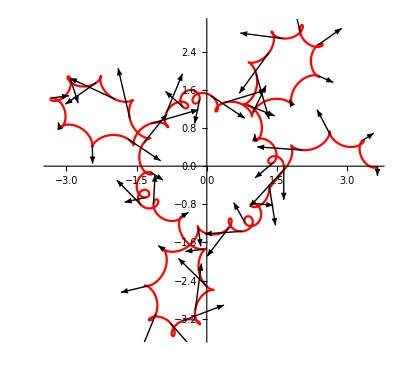

```mathematica
With[{v= Dt[epic[4, tt], tt]},Show[ParametricPlot[epic[4, t], {t, 0, 10π}, PlotStyle -> Red], Graphics[Table[Arrow[{epic[4, t], epic[4, t] + .5(v /.tt -> t)}], {t, 0, 10π, π/5}]]]]
```

We can try to integrate the total path length traversed up to the given time. Since the paths get more ziggy and zaggy as the index increases, we shall again content ourselves with numerical integration. This works fine for points zero to three, but seems to reach some internal limit of Mathematica for point four. Even symbolic computation, when performed under the constraints and limitations of our actual physical machine of Computronic Mk 2000, must ultimately conform to the restrictions of that device, as opposed to running smoothly in some Platonic realm of ideas. No-one has yet built a monument so high that some bird can’t fly over and take a poop on it.

```mathematica
Table[ArcLength[epic[i, t], {t, 0, 10}, Method -> "NIntegrate"], {i, 0, 4}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.95297}. NIntegrate obtained 12.8694 and 0.000110094 for the integral and error estimates.

{0.,4.,5.44149,8.37962,12.8694}

The astronomers of the ancient past who followed the now obsolete geocentric Ptolemaic model of the solar system, in their insistence that all planetary orbits must be circles as their model requires, quickly ran into undeniable discrepancies between the predictions of their model and the actual observations acquired just by looking at the night sky and determining the current positions of the planets. Who would they now believe, their model or their own lying eyes? Trying to explain away these uncomfortable discrepancies, their originally simple models became ever more complex as epicycles were piled upon epicycles. This expression “adding epicycles” is part of the English language to mean that the person or institution that is clinging to some incorrect model of reality keeps augmenting it with ever more desperate ad hoc adjustments that massively increase the complexity of this model for every slight little gain of accuracy, instead of throwing the entire model in the dustbin of history and replacing it with one that depicts reality more accurately.

Expanding our parametric world up to three dimensions again, the function ParametricPlot3D can also render arbitrary parametric surfaces defined by two parameters, canonically named u and v instead of t that is used in one dimension, used by the function to generate all the points of the surface, such as “Cresent” taken from the excellent fractals page of Paul Bourke.

```mathematica
ParametricPlot3D[{2+Sin[2 π  u] Sin[ π  v] Sin[3π v], 2+Sin[2 π  u] Sin[ π  v] Cos[3π v],Cos[2 π  u]Sin[2π v] +4v - 2},{u,0,1},{v,0,1},PlotStyle->{Directive[Specularity[White,50],Texture[ExampleData[{"ColorTexture","CheetahFur"}]]]},Axes->None, Lighting->"Neutral", Boxed-> False, ImageSize -> Medium]
```

-Graphics3D-

As the epicycloid example already demonstrated, there is no limit to the infinite variety of screws and twists that you could define parametrically. (As a further exercise on this theme, you could modify the epicycloid chain so that the radii are no longer constants, but made of rubber.) For a more familiar shape, the surface of a sphere can be defined with two parameters that correspond to its longitude and latitude. These components can be stretched any which way, and adding or subtracting a small repetitive quantity to the coordinates makes the surface bumpy and more natural and lively to look at.

```mathematica
ParametricPlot3D[{(1+Cos[(v+u)^2]/2)Sin[u] Sin[v]+0.05 Cos[20 v],Cos[u] Sin[v]+0.05 Cos[20 u],Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{ Texture[ExampleData[{"ColorTexture","Ash"}]], Lighting-> Automatic}, Axes->None,Mesh->None, Boxed-> False, ImageSize -> Small]
```

-Graphics3D-

Plot and all its variations produce objects of types Graphics and Graphics3D, which Mathematica will then display graphically. On your screen, these objects are two-dimensional pixel rasters, but internally they are symbolic so that you can zoom in, rotate and transform them without loss of precision. To convert a graphical object explicitly to a two-dimensional image, use the function Rasterize. This allows you to use Mathematica’s vast array of image processing capabilities.

```mathematica
MedianFilter[Rasterize[%], 2]
```

-Graphics-

Coming back to solving equations for a moment, differential equations that include potentially algebraic components can be concisely solved, either symbolically and numerically, with functions DSolve and NDSolve, the behaviour of these functions being analogous to that of the functions Solve and NSolve. However, for quite a few differential equations, an analytical solution simply does not exist, so numerical methods and techniques are more important in this problem domain than they are for mere algebraic equations or symbolic differentiation. First, a simple differential equation that does happen to have an analytical solution. What happens to a system that consists of a single variable whose initial value equals 2 at the time zero, and whose rate of change equals the negation of the square of the value of the system at the given time? The symbolic solution tells us that such a system will converge towards zero as time approaches infinity.

```mathematica
Clear[y,t];
sol = First[DSolve[{y'[t] == -y[t]^2, y[0] == 2}, y, t]]
```

{y→Function[{t},2/(1+2 t)]}

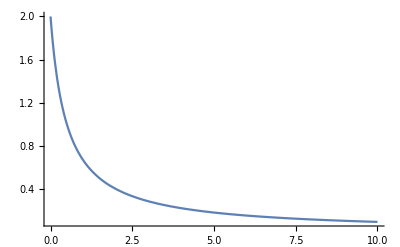

0

```mathematica
Plot[y[t] /. sol, {t, 0, 10}, PlotRange -> All]
Limit[(y[t] /. sol), t -> Infinity]
```

The general analytical solution, whenever found by DSolve, applies for all the values of the independent variable x, even when we plot just a small segment of these values. When solving the differential equation numerically with NDSolve, you must specify the range for the independent variable to investigate the differential equation’s behaviour. The numerical solution presented in the form of an interpolating function will then apply only in that range. If you try to plot it further out, Mathematica will simply extrapolate the interpolating function produced by NDSolve, usually with comical results that have no connection to the underlying system modelled by the original equation.

Instead of just one unknown variable and its derivatives, the system can consist of any number of unknowns and their derivatives. Consider the famous Lotka-Volterra system of differential equations for two unknowns representing the imaginary populations of not-so-slightly idealized rabbits and foxes. (At least these beasts are not spherical and hunt each other in vacuum, as the cows in that old joke about physicists trying to solve problems outside their realm.) The four weight parameters determine how the population of each animal changes depending on the size of the current populations of each animal. When writing formulas that are products of individual symbols, you don’t need to use an explicit multiplication operator, but remember to leave the space in the formulas between the two symbols that you multiply, otherwise Mathematica will treat those two symbols as one compound symbol, and the results will be very strange.

```mathematica
Clear[f, r];
α = 3; β = 1/2; γ = 5; δ = 1/2;
lvsol = NDSolve[{r'[t] == r[t](α -β f[t]), f'[t] == -f[t](γ - δ  r[t]), f[0] == 1, r[0] == 10}, {r[t], f[t]}, {t, 0, 10}]
```

{{r[t]→InterpolatingFunction[{{0., 10.}}, <>][t],f[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

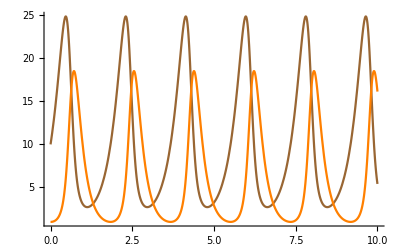

```mathematica
Plot[{r[t]/.lvsol, f[t]/.lvsol}, {t, 0, 10}, PlotRange ->All, PlotStyle->{Brown, Orange}]
```

As you can see from the plot, especially if you further decreased the parameter α, the birth rate of rabbits, the Lotka-Volterra model is unrealistic in that the population of rabbits can and will bounce back from almost zero even when there is a large population of foxes around at the same time, instead of the species going extinct. This is because unlike in the real world, the numbers of foxes and rabbits in these equations are not constrained to be integers, as these populations are assumed to be large enough in that the approximation with real numbers is close enough to truth.

In the model that consists of two functions for the two existing species that populate this artificial microworld, one of these species being the prey and the other one being its predator, all solutions of Lotka-Volterra equations can be proven to be periodic, but they allow no simple analytical solution that could be expressed symbolically. This model could also be generalized to three or more species whose effect on other species population growth could be either symbiotic, competitive or predatory, for even more interesting behaviour.

The previous plot shows how the system evolves over time when started from a particular starting point, but doesn’t tell us anything about what would have happened if the initial number of foxes had been, say, twice as many as it were in that calculation. The function StreamPlot can be used to sketch the directional lines of any vector field. In this case, we use it to plot the partial derivatives for the numbers of foxes and rabbits as arrows in two dimensions, to get a rough idea of how the system will evolve when started at any given point. (Since the system is Markovian in that it has no memory and is time-homogeneous so that the change at any given time depends only on the numbers of foxes and rabbits, the starting point will uniquely determine its entire future trajectory.) The direction vectors revolve around an equilibrium point where the numbers of both foxes and rabbits remain constant, the differentials of both functions being zero at that point and the direction arrow degenerating into a single point.

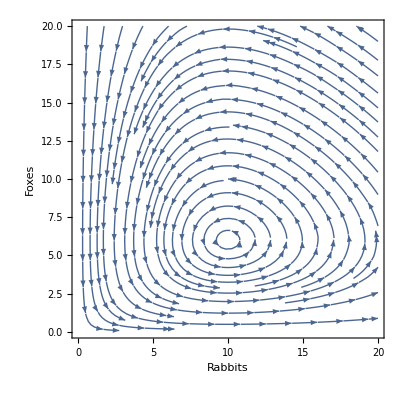

```mathematica
StreamPlot[{r(α - β f),-f(γ-δ r)}, {r, 0, 20}, {f, 0, 20}, PlotRange -> {{0, 20}, {0, 20}},FrameLabel-> {"Rabbits", "Foxes"}]
```

Where is this equilibrium point? (Other than the trivial equilibrium point at the origin where both populations are extinct and cannot grow or shrink, of course.) The location of the equilibrium depends on the constants α et al. defined above. Let’s solve it by making both differentials to equal zero, and zoom in around the equilibrium point.

```mathematica
Solve[{r(α - β f) == 0, -f(γ-δ r) ==0}, {r, f}]
```

{{r→0,f→0},{r→10,f→6}}

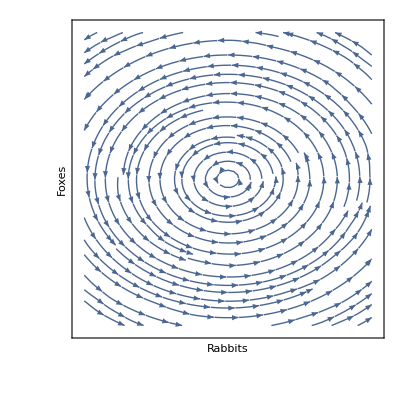

```mathematica
StreamPlot[{r(α - β f),-f(γ-δ r)}, {r, 9.99, 10.01}, {f, 5.99, 6.01}, FrameLabel-> {"Rabbits", "Foxes"}, FrameTicks -> None]
```

It’s hard to tell with such imprecise sampling what exactly is going on in there, but of course no amount of sampling would get us down to the infinitesimal. (The stability properties of this equilibrium point could be analyzed by looking at the eigenvalues of the Jacobian matrix of the partial derivatives of the functions f and r, for those readers who are interested of that kind of stuff.)

When doing differentiation with either Solve or NDSolve, the differential equations are allowed to be of any order. For example, here is a third order differential equation that ends up having a solution that grows exponentially, so we shall plot it in logarithmic scale to make a bit more sense of it. In general, to solve a differential equation of the order n, you need to provide the initial values to the derivatives up to n - 1 to force the unique solution exist numerically. (Symbolically solved equations can produce infinite families of parametric solutions, whose new parameter variables C[k] are then made up on the spot by Mathematica.)

```mathematica
DSolve[{y'''[t] -y''[t] +y'[t] +2 y[t] == .5, y[0] == 1}, y, t]
```

{{y→Function[{t},-1. ⅇ^(-0.810536 t) (-0.25 ⅇ^(0.810536 t)-1. C[1]-0.75 ⅇ^(1.7158 t) Cos[1.28374 t]+1. ⅇ^(1.7158 t) C[1] Cos[1.28374 t]-1. ⅇ^(1.7158 t) C[2] Sin[1.28374 t])]}}

```mathematica
NDSolve[{y'''[t] -y''[t] +2y'[t] +6 y[t] == 4, y[0] == 1, y'[0] == -2, y''[0] == -4}, y, {t, 0, 100}]
```

{{y→InterpolatingFunction[{{0., 100.}}, <>]}}

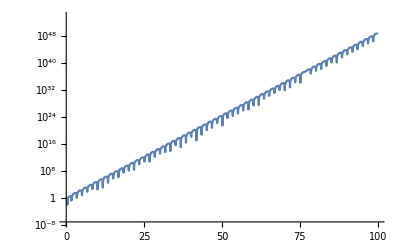

```mathematica
LogPlot[Abs[y[t]] /. %, {t, 0, 100}, PlotRange -> All]
```

Differential equations could even have hundreds or thousands of unknown quantities. So that you don’t need to make up a separate variable name for every unknown quantity and write the equations for it, you can just keep all these variables in one vector under a single symbolic name. To illustrate this technique, we can plot out a very simple orbital model where a point mass has a position x[t] that is a vector of three components, one for each of its three spatial coordinates. Residing stationary at the origin, there is a much larger mass that the point mass is gravitationally attracted to. Solving for x[t] in a second-order differential equation (since the acceleration by the Newton’s law of gravity is the second differential of position x[t]) with the simplifying assumption that the larger mass remains stationary (calculated properly, this large mass would wobble around the shared center of gravity of both masses that would remain spatially located somewhere inside the larger mass) produces an orbital path that needs no epicycles.

```mathematica
ClearAll[x,t];
NDSolve[{x''[t]== -x[t]/Norm[x[t]]^2, x[0] == {0, 3, 1}, x'[0] == {1, -1/2, 0}},x, {t, 0, 100}]
Show[ParametricPlot3D[{x[t]/. %}, {t, 0, 100}, Axes -> False], Graphics3D[Ball[{0,0,0}, .1]]]
```

{{x→InterpolatingFunction[{{0., 100.}}, <>]}}

-Graphics3D-

You can try modifying the initial position x[0] and initial velocity x’[0] of this point mass and observe their effect on the orbit. (Make sure to give the point mass at least some sideways velocity so that it won’t fall directly into the origin where the equations would reach a singularity when dividing by zero, and the numerical differentiation would crash with an error message.) To model a system that consists of n bodies gravitationally attracted to each other, you need 3n variables for these positions, and must provide as boundary conditions the initial values of both these positions and their velocities. However, as is well known in physics, this necessarily must be done numerically except in certain special cases, since there does not exist a general analytical solution for a gravitational system that has three or more bodies.

The previous curves have been quite squiggly but not yet properly chaotic in the sense that they would be extremely sensitive to the initial values of their variables. Most mathematics that most people have ever seen is not chaotic, as can be seen from the following little experiment. Pick randomly some problem in your high school math, physics or chemistry textbook (actually, it most likely wouldn’t matter which one, even if you chose this problem freely to prove me wrong), and then solve it, just like your old science teacher taught you to do it. However, unlike back when you just moved to the next problem, you should now next do something that the textbook didn’t ask you to do: change each numerical parameter of that same problem a teeny little bit, and solve that same problem again using these new perturbed numerical values. I bet you now dollars to donuts that the result that you got the second time will only be slightly different from the first result using the original numerical values. The calculation that you performed to solve the problem was therefore not chaotic, but behaves nicely in the sense that small differences in the initial condition will create only a small difference in the second result.

However, most of our physical and especially social reality, or at least their interesting parts, simply doesn’t behave that way. Small differences in the initial state will soon enough blow up into big differences in the result. As an analogy, consider a pool table and a tiny difference in the angle or force that your cue hits the ball. This tiny difference might not affect the trajectory and the final position of a single ball that much, were that ball alone on the table. But in the system that consists several balls and iterated collisions, even a tiny difference in the direction or velocity of the initial ball will create a big difference in the direction that the second ball takes, which will then turn into a massive difference of hit and miss for the third and other balls. Like all interesting systems, a pool table amplifies initial small differences to something that is unpredictable, since given enough hits between the balls, even the small difference in the gravity field caused by the direction of the Sun would affect the end result. The same principle of “loose wiring” applies to all other interesting games that people have invented throughout the history.

Historically, the first system to express such massive sensitivity to initial conditions (and as a side effect, coined the famous term “butterfly effect”) was found by the meteorologist Edward Lorenz in 1963. Trying to model an atmospheric phenomenon with three parameters and three equations, he accidentally discovered that in his simple system of differential equations, a tiny change in the initial values (accidentally caused by repeating some earlier calculations using rounded decimal values of the output instead of the more precise values stored internally by the calculator) caused the results to diverge. The system is shown below as a differential equation of three variables x, y and z and three parameters ρ, σ and β, evaluated twice with a small change in the initial values.

```mathematica
ClearAll[x,y,z];
lorenz[ρ_, σ_, β_] := NDSolve[{
x'[t] == σ (y[t]-x[t]),
y'[t] == x[t](ρ - z[t]) - y[t],
z'[t] == x[t]y[t] - β z[t],
x[0] == 5, y[0] == 5, z[0] == 5
},{x[t], y[t], z[t]}, {t, 0, 15}];
s1 = lorenz[28, 10, 8/3];
s2 = lorenz[28.2, 10.2, 8/3-0.2];
ParametricPlot3D[{{x[t], y[t], z[t]} /.s1, {x[t], y[t], z[t]} /.s2}, {t, 0, 15}, PlotRange -> All]
```

-Graphics3D-

The fact that even this simple model of weather is hopelessly chaotic lays waste to all dreams of being able to accurately model weather using any computational model whatsoever. Since all measurements of any physical system are necessarily slightly inaccurate, any model can predict the future evolution of the system only so far ahead until it has to succumb to the inevitable chaos. Increasing the precision of measurements will merely postpone this chaos, but can only do that up to some limit determined by the Lyapunov exponent of that system. In any chaotic system, there is no measurement error above zero that would not eventually lead to divergence. On the other hand, we should also note that the chaos of the Lorenz system is still tightly controlled in the sense that the curve will traverse only a small part of the possible space of values along its strange attractor. Even if the weather is a chaotic system, it is still a pretty safe bet to say that most of its possibilities are unreachable starting from the current partially known state of the system, such as a snowstorm in Sahara or a tornado in Svalbard. The same phenomenon of chaotic unpredictability that is guaranteed to remain within certain bounds of its chaotic attractors is exploited in many forms of gambling with dice, cards, roulette, pachinko and a myriad other games. The house will always win, unless the player changes the rules of the game to change the underlying equations.

Unlike physical systems that are subject to some measurement error, the data inside computers is in principle fully known and exact. However, predictions of the future behaviour of any system, even if perfectly deterministic and precise, are still logically impossible if the predictor is itself a part of the system that it would try to predict. If such prediction were possible in time faster than merely letting the system run its course and watching what happens, the predictor could create a logical contradiction by first making the prediction and then intentionally steering the system to do the exact opposite! Since logical contradictions are not supposed to be possible, the only way to get out of this paradox is to realize that in such situation, the act of prediction is in general impossible.

Alan Turing realized this back in the year 1936, before any physical computers had even been built, and proved that it is impossible to solve the halting problem algorithmically. Halting problem is the question whether the execution of the given computer program with given input will eventually halt or whether the execution will go on forever. The problem is well posed in the sense that in a deterministic computer, the answer has to be one or the other, but never both or neither. A program will either run forever or halt, even if we will not remain alive long enough to actually watch either possibility realizing, the same way that the number 2^57885161-1 is known to be a prime number even though we cannot possibly count that high using our fingers and toes, or any physically available number of pens and sheets of scrap paper.

The proof is especially easy to construct in terms of Mathematica expressions and their simplifications because of the homoiconic nature of the language. Assume that there exists a computable function Halt[expr] that, for any argument expr, can always be simplified in finite time to either True or False and never to anything else, the choice of the two results depending on whether the simplification of its argument expression expr will end in finite time. Define somewhere also an expression called forever whose exact content makes no difference as long as this expression is such that its simplification will never terminate. To swing the vorpal blade directly through the gizzard of this beast, we define the following function troll[expr] that first asks whether the simplification of expr[expr] will terminate, and then do the opposite in that if expr[expr] terminates, troll[expr] will go on forever, and if expr[expr] goes on forever, troll[expr] will terminate with some result whose exact value doesn’t really even matter.

```mathematica
troll[exp] :=
If[Halt[exp[exp]], forever, 42];
```

Pray tell: what would now happen in the simplification of the expression troll[troll] that makes the function troll eat its own metaphorical tail? This function would first use Halt to ask whether the simplification of troll[troll] will terminate, and then do the exact opposite. Therefore whatever Halt[troll[troll]] answers, that particular answer is wrong. In other words, Halt is not an expression that will reliably check whether the simplification of its parameter expression will terminate, as proven by the fact that we found one expression (of the infinitely many such expressions possible, in fact) that tricks it into giving the wrong answer. Sure, the function Halt might get the answer right for infinitely many other expressions, but not for this one that was specifically constructed to create this contradiction. Since Halt was allowed to be any expression that could be chosen freely by any crank who denies the truth of this construction, no expression can exist that will solve the halting problem for every arbitrary expression. The halting problem can be solved in many special cases, but not in the general case.

This situation is actually soon revealed to be a lot worse, since the halting problem could be mechanistically converted to many other seemingly simple questions about the behaviour of computer programs so that the result of the original halting problem is the same as the result of the converted problem. Since we know that the halting problem is impossible to solve algorithmically in general, all these other problems must therefore also be impossible to solve in general. This observation and its careful proof is known in the theory of computation as Rice’s theorem. Many of these problems are algorithmically solvable in special cases, but none of them can be algorithmically solvable in general.

## Entities and properties

Coming back to Earth from the heavenly spheres of abstract elegance that we ascended towards in more ways than one, Mathematica is tightly connected to Wolfram Alpha knowledge base and its natural language interface. You can make Wolfram Alpha queries and free form natural language queries directly from the notebook either by creating an appropriate type input cell, or by starting an input cell with the symbol = or ==.

WolframAlphaQueryParseResults

Toronto

Entities are symbolic expressions that have the head Entity. Each entity represents some object that exists in the real world outside Mathematica. The entity represents all its associated properties in a form that can be used to perform computations about that entity. The front end of Mathematica displays entities as rounded rectangles with a red border and yellow background, but like everything else, internally these entities are still symbolic expressions.

```mathematica
toronto =%;
toronto // FullForm
```

Entity["City",List["Toronto","Ontario","Canada"]]

To acquire more entities, you can use the curated knowledge bases built in the language itself. As you can find out from the Mathematica documentation, there exists a whole bunch of SomethingData functions that cover all sorts of stuff between the heavens and the Earth that is dreamt in our philosophies.

```mathematica
betelgeuse = StarData["Betelgeuse"]
betelgeuse["Density"]
```

Betelgeuse

7.9×10^-9

To access the individual properties of some entity, use the function EntityValue, or as seen in the previous example, simply treat the entity as a function that operates on a string argument that contains the name of that property. Accessing properties of entities can be sluggish the first time, as the corresponding entity database must be first downloaded from the Wolfram Alpha servers. Once queried, the data of course remains cached locally on your computer to allow future queries about those same entities to be more efficient.

```mathematica
EntityValue[toronto, "Population"]
toronto["AdministrativeDivision"]
```

2731571

Ontario, Canada

```mathematica
EntityValue[betelgeuse, "Color"]
```

color red:1. green:0.75 blue:0.5

The value of some property of an entity can be any symbolic expression, including another entity or a list of entities, so these entities of all types form a complex and ever-growing graph of relationships depicting the connections that these entities have to each other. A property of some entity can even be a list of substitution rules from entities to other things.

```mathematica
EntityValue[toronto, "AirportCodes"]
```

{Armour Heights Field,Barker Field,Cardinal Couriers Heliport,Buttonville,Toronto City Centre Airport,Toronto Pearson International Airport,Downsview Airport,De Lesseps Field,Leaside Aerodrome,Markham Airport,Markham Stouffville Heliport,Tarten Heliport,Toronto Aerodrome,Toronto (Hospital For Sick Children) Heliport,Toronto (Mississauga Credit Valley Hospital) Heliport,Toronto (St. Michael's Hospital) Heliport,Toronto (Sunnybrook Medical Centre) Heliport,Willowdale Airfield,Wilson's Heliport}

```mathematica
EntityValue[Entity["Language", "Finnish"], "Speakers"]
```

{Finland→4700000,Russia→17000,Sweden→200000}

To find out the list of all properties that some entity has to offer, you can either use the function EntityProperties, or just get the value of the property “Properties”. For many entities, this list will end up being pretty long, so we shall just take a brief look at the first ten elements. (The list function Take gives you the desired number of elements starting from the beginning of the list, and is often handy in making a quick sanity check of the results of computations that produce long lists.)

```mathematica
Take[EntityProperties[toronto], 10]
```

{administrative region,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,airport codes}

Notice that the properties are themselves entities, so they can have properties of their own, accessed the same way. Entities are further grouped to entity classes, which are also themselves entities. Entity classes are easily accessible with the functions EntityClassList and EntityClass. Each entity (or entity class) can simultaneously belong to any number of entity classes, reflecting the idea that instead of reality being hierarchical, it is tagged so that everything is miscellaneous.

```mathematica
Take[EntityClassList["Country"], 10]
```

{Africa,African Caribbean and Pacific Group,African Development Bank,African Union,Agency for the Prohibition of Nuclear Weapons in Latin America and the Caribbean,Agency of Cultural and Technical Cooperation,Alliance of Small Island States,The Americas,Andean Community of Nations,Antarctica}

```mathematica
africa = EntityClass["Country", "Africa"]
```

Africa

As you can see in the examples above, entity classes are themselves entities, but to inform you about this fact, Mathematica displays them with some red dots in front of the name to slyly make them visually different. Evaluating EntityValue without arguments gives you a good starting point for entity classes.

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,Alphabet,AmusementPark,AmusementParkRide,AnatomicalFunctionalConcept,AnatomicalStructure,AnatomicalTemporalConcept,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,BasicFoodGroup,Beach,BoardGame,Book,Bridge,BroadcastStation,BroadcastStationClassification,Building,Canal,Castle,CatBreed,Cave,Cemetery,Character,Chemical,City,Cloud,CognitiveTask,Color,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Element,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FictionalCharacter,FileFormat,Financial,FiniteGroup,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gene,GeographicRegion,GeologicalLayer,GeologicalPeriod,GivenName,Glacier,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,MannedSpaceMission,MathematicalFunction,MathWorld,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,Mine,Mineral,MinorPlanet,Mountain,Movie,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicalInstrument,MusicWork,MusicWorkRecording,Mythology,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearReactor,NuclearTestSite,Ocean,OilField,Park,Particle,ParticleAccelerator,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalConstant,PhysicalSystem,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,Polyhedron,PopularCurve,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,Satellite,SchoolDistrict,Ship,Shipwreck,SNP,SolarSystemFeature,Solid,Source,SpaceCurve,Species,SportMatch,SportObject,Stadium,Star,StarCluster,Supernova,Surface,Surname,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAFoodGroup,Volcano,Waterfall,WeatherStation,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptType,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

To crack open an entity class to find out the delicious entities it contains, use the function EntityList.

```mathematica
Take[EntityList[africa], 10]
```

{Algeria,Angola,Benin,Botswana,Burkina Faso,Burundi,Cameroon,Cape Verde,Central African Republic,Chad}

Entities and their properties can be used in computations. To finish up and give you a taste of that, here are the ten largest African countries sorted by area, using the list operations of the next lesson. The function Map is first used to project each entity to a pair that contains only its name and area, and this list is then sorted with an anonymous function that uses only the second element of this pair to compare them. The following query gives us the list of countries in Africa sorted by their area, from which we Take the first ten.

```mathematica
Grid[Take[Sort[Map[{EntityValue[#, "Name"], EntityValue[#, "Area"]}&, EntityList[africa]], (#1[[2]] > #2[[2]])&], 10]]
```

Algeria | 2.38174×10^6
Democratic Republic of the Congo | 2.34486×10^6
Sudan | 1.88607×10^6
Libya | 1.75954×10^6
Chad | 1.284×10^6
Niger | 1.267×10^6
Angola | 1.2467×10^6
Mali | 1.24019×10^6
South Africa | 1.21909×10^6
Ethiopia | 1.12713×10^6